Last modified on: Thursday, July 12, 2018 at 22:31

Author Info

Euan Ong

Dariia Porechna

End of Camp Presentation Content

Using Machine Learning Models for Accelerometer-based Gesture Recognition

1. Investigate methods of asynchronous communication between a phone and the Wolfram Language
2. Implement a gesture recognition system based around phone accelerometer data using machine learning

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

1. Asynchronous Communication
	Two methods: UDP sockets (needs JLink) and the Wolfram Channel[] function (XHR or Pub-Sub communication). UDP sockets have slightly less lag than the Channel[] function, but are more difficult to use due to more moving parts
2. Gesture Recognition
	Although data is in the form of a time series, using transfer learning with a convolutional neural network (VGG-16) works well on rasterised graph images.
gestClassifier/@{-Graphics-,-Graphics-,-Graphics-}
{1,2,3}

- Integrate gesture classification system with ChannelDeploySensorPage and deploy to the cloud
- Investigate the feasibility of using an RNN or an LSTM for gesture classification
- Add an API to trigger actions based on gestures
- Explore other applications of gesture recognition (e.g. walking style, safety, sign language recognition)

Additional Code Content

c = ChannelDeploySensorPage[ProcessData]
Dynamic[ListLinePlot[ToExpression/@Reverse[Take[Reverse[#["Values"]],UpTo[100]]]&/@c⟦3⟧["TimeSeries"]⟦2;;4⟧,PlotRange→{All,{-20,20}},PlotStyle->{Red, Green, Blue}]]

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

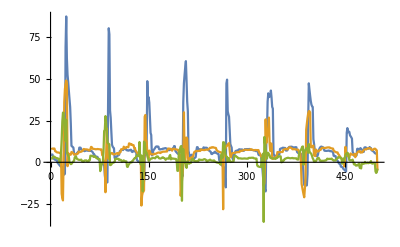
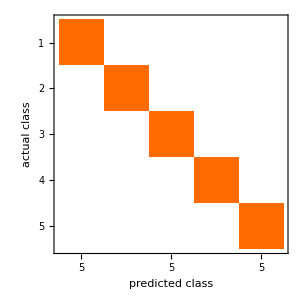
As technology advances, we are constantly seeking new, more intuitive methods of interfacing with our devices and the digital world; one such method is gesture recognition. Although touchless human interface devices (kinetic user interfaces) exist and are in development, the cost and configuration required for these sometimes makes them impractical, particularly for mobile applications. A simpler method would be to use devices the user already has on their person - such as a phone or a smartwatch - to detect basic gestures, taking advantage of the wide array of sensors included in such devices. In an attempt to assess the feasibility of such a method, methods of asynchronous communication between a mobile device and the Wolfram Language are investigated, and a gesture recognition system based around an accelerometer sensor is implemented, using a machine learning model to classify a few simple gestures from mobile accelerometer data.

Investigating Methods of Asynchronous Communication
To implement an accelerometer-based gesture recognition system, we must devise a suitable means for a mobile device to transmit accelerometer data to a computer running the Wolfram Language (WL). On a high level, the WL has baked-in support for a variety of devices - specifically the Raspberry Pi, Vernier Go!Link compatible sensors, Arduino microcontrollers, webcams and devices using the RS-232 or RS-422 serial protocol (http://reference.wolfram.com/language/guide/UsingConnectedDevices.html); unfortunately, there is no easy way to access sensor data from Android or iOS mobile devices.

On a low level, the WL natively supports TCP and ZMQ socket functionality, as well as receipt and transmission of HTTP requests and Pub-Sub channel communication. We investigate the feasibility of both methods for transmission of accelerometer data:
Socket Transmission
Although a number of tutorials are available for transmission of sensor data from an iOS device to the WL (http://community.wolfram.com/groups/-/m/t/344278), no such resources are as yet available for Android devices - there is some support for exporting Android sensor data to the Wolfram Data Drop (http://community.wolfram.com/groups/-/m/t/461190), however this has extremely high latency (data upload is every 2 minutes) and so is not suitable for gesture recognition. 

On the Google Play Store, there exist a number of Android apps which can transmit live sensor data to a computer over UDP sockets - for instance, “Sensorstream IMU+GPS” (https://play.google.com/store/apps/details?id=de.lorenz_fenster.sensorstreamgps). Unfortunately, the WL does not support receipt and transmission of data over UDP sockets - while there exists a Socket library, as of 2018 this is only capable of dealing with TCP. Thus, to use UDP sockets in the WL, we must implement our own library using JLink to access Java socket packages from the WL. (Credit is due to http://community.wolfram.com/groups/-/m/t/344278 - the code here was slightly outdated so had to be modified.)
JLink and Sockets
To send accelerometer (or other sensor) data from your phone to Wolfram over UDP sockets:

1. Install the “Sensorstream IMU+GPS” app
2. Ensure the sensors you want to stream to Wolfram are ticked on the ‘Toggle Sensors’ page.  (If you want to stream other sensors besides ‘Accelerometer’, ‘Gyroscope’ and ‘Magnetic Field’, ensure the ‘Include User-Checked Sensor Data in Stream’ box is ticked. Beware, though - the more sensors are ticked, the more latency the sensor stream will have.)
3. On the “Preferences” tab:
a. Change the target IP address in the app to the IP address of your computer (ensure your computer and phone are connected to the same local network)
b. Set the target port to 5555
c. Set the sensor update frequency to ‘Fastest’
d. Select the ‘UDP stream’ radio box
e. Tick ‘Run in background’
4. Switch stream ON before executing code. (nb. ensure your phone does not fall asleep during streaming - perhaps use the ‘Caffeinate’ app (https://play.google.com/store/apps/details?id=xyz.omnicron.caffeinate&hl=en_US) to ensure this.)
5. Execute the following WL code (in part from http://community.wolfram.com/groups/-/m/t/344278):
QuitJava[];
Needs["JLink`"];
InstallJava[];
Initialise JLink
udpSocket=JavaNew["java.net.DatagramSocket",5555];
Initialise a socket connection - ensure 5555 is the target port set
readSocket[sock_,size_]:=JavaBlock@Block[{datagramPacket=JavaNew["java.net.DatagramPacket",Table[0,size],size]},sock@receive[datagramPacket];
datagramPacket@getData[]]
Function that reads size bytes of a function.
listen[]:=record=DeleteCases[readSocket[udpSocket,1200],0]//FromCharacterCode//Sow;
Function that reads from the socket, processes data and ‘sows’ it to be collected later
results={};RunScheduledTask[AppendTo[results,Quiet[Reap[listen[]]]];If[Length[results]>700,Drop[results,150]],0.01];
Initialises the results list and repeatedly appends accelerometer data to it every 0.01 seconds - if the list is over 700 elements long, the 150 oldest elements (at start of list) are removed.
stream:=Refresh[ToExpression[StringSplit[#[[1]],","]]& /@ Select[results[[-500;;]],Head[#]==List&],UpdateInterval→ 0.01]
Initialises the stream list to be refreshed every 0.01 seconds with the most recent 500 elements of results. Each element of results is a string of transmitted socket data (e.g. “225585.00455, 3,  -1.591,  8.624,  5.106, 4,  -0.193, -0.690, -0.072”) - this is split into a list of strings {“225585.00455”, ”3”, ”-1.591”...} and each string is converted to a numerical expression.
Stream now contains the 500 most recent accelerometer readings, stored in an array. The values of Stream will be updated whenever the variable is used within a Dynamic. (Note that, with the default sensors enabled - the first three boxes ticked on the Toggle Sensors tab - the x, y and z coordinates of the accelerometer can be accessed at elements 3, 4 and 5 in each list in the array. (e.g. to access the most recent accelerometer reading, run stream⟦-1,3;;5⟧)
The accelerometer data can then be visualised using a ListLinePlot:
While[Length[results]<500,Pause[2]];Dynamic[Refresh[ListLinePlot[{stream[[All,3]],stream[[All,4]],stream[[All,5]]},PlotRange→All],UpdateInterval→0.1]]
-Graphics-
The ‘pulses’ (i.e. shaking the phone) were carried out every second; from this it is evident that the frequency of data transmission is 50 Hz (i.e. data is sent every 0.02 seconds).
To get the most recent accelerometer data, run
Dynamic[stream[[-1,3;;5]]]
To end socket transmission, turn off the stream on the app, run
RemoveScheduledTask[ScheduledTasks[]];
udpSocket@close[];
QuitJava[];
Ensure the process ‘JLink’ is quit in Task Manager / Activity Monitor etc - if it is not closed properly, you will be unable to create another socket from that port.
Channel Transmission
Channel Basics
An alternative way to send data from a phone to the Wolfram Cloud is by using the Channel framework. Introduced in version 11 of the Wolfram Language. the Channel framework allows asynchronous communication between Wolfram sessions as well as external systems, with communication being brokered in the Wolfram Cloud. A key point to note about the Channel framework is that it is based on a publish-subscribe model, allowing messages to be sent and received through a ‘channel’ rather than pairing specific senders and receivers. <This makes it easy for users ?...>

Setting up a channel is as easy as connecting to the Wolfram Cloud
CloudConnect[];
and typing
current="";
Func[x_]:=current=x;
listener=ChannelListen["NameOfChannel",Func[#Message]&, Permissions→"Public"]
ChannelListener[…]
Here, Func is a function that will be called each time the channel receives a message (the message is supplied as an argument to the function) - it simply sets the variable ‘current’ to the data last sent to the channel (in the form of key-value pairs - e.g. <|x=3, y=4, z=1|>. To make the channel accessible to other users, ensure the channel has Permissions set to Public.
To delete the channel (useful when debugging), call
RemoveChannelListener[listener];

One particularly useful feature of the Channel is that it has built-in support for receiving and parsing HTTP requests - simply send a GET request to the channel URL (given by listener[“URL”]) and the WL will automatically parse the parameters and make the data available to the user: 

For instance, if we send an HTTP GET request to https://channelbroker.wolframcloud.com/users/<your Wolfram Cloud email address>/NameOfChannel and append the parameters “operation=send” (indicates data is being sent to the channel) and “test=5”:
BaseURL=listener["URL"]
"https://channelbroker.wolframcloud.com/users/euan.l.y.ong@gmail.com/NameOfChannel"
Params = "?operation=send&test=5";
URLRead[HTTPRequest[BaseURL<>Params,<|Method->"Get"|>]]
HTTPResponse[…]
The variable ‘current’ has now been updated and contains the key-value pair ‘test->5’ which we just sent to the channel.
current
<|"test"→"5"|>
current[["test"]]
"5"
An alternative way of viewing the data from the channel is to call
listener["TimeSeries"]
<|"test"→TimeSeries[…]|>
This allows the data sent to the channel to be stored as a time series, which can be useful in applications such as collecting time-based sensor data.
Transmission of Sensor Data over Channels
As demonstrated earlier, a nice feature of Channels is that data can be sent to the Wolfram Language over HTTP - instead of fiddling with JLink and sockets (which tend to be laggy and break easily), one can simply create a web page that streams sensor data to a channel.

For Android devices (running Google Chrome), there exist a range of built-in sensor APIs giving a web page access to raw accelerometer, gyroscope, light sensor and magnetometer data, and processed linear acceleration (i.e. total acceleration experienced by a device disregarding that produced by gravity), absolute orientation and relative orientation sensors. Documentation for these sensors exists online at https://developers.google.com/web/updates/2017/09/sensors-for-the-web.

Unfortunately, for iOS devices there does not exist an easy way to access sensors from the web - although one can use DeviceMotion events (https://developers.google.com/web/fundamentals/native-hardware/device-orientation/), the data these give can vary significantly from browser to browser (e.g. different browsers might use different coordinate systems), so training a machine learning model on gesture data produced by this method would require either retraining a model for each browser or significant processing of data based on browser.

However, there is another solution - namely, the gyronorm.js API (https://github.com/dorukeker/gyronorm.js), which claims to return ‘consistent [gyroscope and accelerometer] values across different devices’. Using this, we construct a simple web page to transmit accelerometer data to a Wolfram Language channel called ‘Sensors’: (While the following code focuses on extracting accelerometer data, it is a trivial task to change the sensor being polled to read, for instance, gyroscope data in the Wolfram Language instead.)
<!DOCTYPE html>
<html lang=en>
<meta charset=UTF-8>
<title>Sensors</title>
<script src=https://cdn.jsdelivr.net/npm/gyronorm@2.0.6/dist/gyronorm.complete.min.js></script>

<script>
function makeXHR(x,y,z){
	var t=Date.now();
	r=new XMLHttpRequest;
	r.withCredentials=true;
	var i="https://channelbroker.wolframcloud.com/users/euan.l.y.ong@gmail.com/Sensors?operation=send&time="+t.toString()+"&x="+x.toString()+"&y="+y.toString()+"&z="+z.toString();
	r.open("GET",i,!0);
	r.send()
}

function init(){
	//Explanations are from the GyroNorm GitHub page. (https://github.com/dorukeker/gyronorm.js/)
	var n={
		frequency:100, //send values every 100 milliseconds
		gravityNormalized:!0, // Whether or not to normalise gravity-related values
		orientationBase:GyroNorm.WORLD, // ( Can be Gyronorm.GAME or GyroNorm.WORLD. gn.GAME returns orientation values with respect to the head direction of the device. gn.WORLD returns the orientation values with respect to the actual north direction of the world. )
		decimalCount:2, // How many digits after the decimal point to return for each value
		logger:null,
		screenAdjusted:!1
	};
	t=new GyroNorm;
	t.init(n).then(function(){
		t.start(function(data){
			makeXHR(data.dm.x,data.dm.y,data.dm.z)
			//Other possible values to substitute for data.dm.x, data.dm.y, data.dm.z are:
			// data.do.alpha	( deviceorientation event alpha value )
		    // data.do.beta		( deviceorientation event beta value )
		    // data.do.gamma	( deviceorientation event gamma value )
		    // data.do.absolute	( deviceorientation event absolute value )

		    // data.dm.x		( devicemotion event acceleration x value )
		    // data.dm.y		( devicemotion event acceleration y value )
		    // data.dm.z		( devicemotion event acceleration z value )

		    // data.dm.gx		( devicemotion event accelerationIncludingGravity x value )
		    // data.dm.gy		( devicemotion event accelerationIncludingGravity y value )
		    // data.dm.gz		( devicemotion event accelerationIncludingGravity z value )

		    // data.dm.alpha	( devicemotion event rotationRate alpha value )
		    // data.dm.beta		( devicemotion event rotationRate beta value )
		    // data.dm.gamma	( devicemotion event rotationRate gamma value )
		})
	})
}
window.onload=init;
</script>
</html>
This webpage, when opened on an Android or iOS phone, will stream data to the ‘Sensors’ channel, sending a new HTTP request every 100 milliseconds. (Decreasing the ‘frequency’ leads to more frequent results, but can cause atrocious levels of lag.)
Producing the ChannelDeploySensorPage function
Although this webpage allows accelerometer data to be transmitted from a phone to a computer, for it to be used it must be deployed on a server. To change, for instance, the channel name, one would need to edit the file on the server itself, which can quickly become a tiresome process. Thus, we developed a function which autogenerates the required HTML code and stores it in the Wolfram Cloud as a CloudObject where it can easily be accessed. The function also outputs a QR code, to allow mobile users to quickly navigate to the web page. (The argument func is simply the function to be called whenever the channel receives a new point of data from the phone.)
ChannelDeploySensorPage[func_]:=Module[{listener,listenerurl,SensorHTML,c,url,u},
CloudConnect[];
listener=ChannelListen["Sensors",func[#Message]&,Permissions→"Public"];
listenerurl = listener["URL"];
SensorHTML="<!DOCTYPE html><html lang=en><meta charset=UTF-8><title>Sensors</title><script src=https://cdn.jsdelivr.net/npm/gyronorm@2.0.6/dist/gyronorm.complete.min.js></script><script>function makeXHR(n,t,o){var e=Date.now(),r=(Math.random(),new XMLHttpRequest);r.withCredentials=!0;var i=""<>listenerurl<>"?operation=send&time="+e.toString()+"&x="+n.toString()+"&y="+t.toString()+"&z="+o.toString();r.open("GET",i,!0),r.send()}function init(){var n={frequency:100,gravityNormalized:!0,orientationBase:GyroNorm.WORLD,decimalCount:2,logger:null,screenAdjusted:!1},t=new GyroNorm;t.init(n).then(function(){t.start(function(n){makeXHR(n.dm.x,n.dm.y,n.dm.z)})})}window.onload=init</script>";
(* To use with other sensors, copy the HTML code in the previous section and replace https://channelbroker.wolframcloud.com/users/euan.l.y.ong@gmail.com/Sensors with "<>listenerurl<>" *)
c = CloudExport[SensorHTML,"HTML",Permissions→"Public"];
u=URLShorten[c[[1]]];
Return[{u,BarcodeImage[u,"QR"],listener}]
] 
Example Usage: (using the Func function from above)
c = ChannelDeploySensorPage[Func]
{"https://wolfr.am/w8fPPb4i",-Graphics-,ChannelListener[…]}
A user can now simply scan the above QR code and sensor data will be streamed from their phone to the computer.
The data can be viewed as a time series as follows:
c[[3]]["TimeSeries"]
<|"time"→TimeSeries[…],"x"→TimeSeries[…],"y"→TimeSeries[…],"z"→TimeSeries[…]|>

The accelerometer data can also be plotted with the following Dynamic: (red --> x, green --> y, blue --> z)
Dynamic[ListLinePlot[ToExpression/@Reverse[Take[Reverse[#["Values"]],UpTo[100]]]&/@c⟦3⟧["TimeSeries"]⟦2;;4⟧,PlotRange→{All,{-50,50}},PlotStyle->{Red, Green, Blue}]]
When you’re done, delete the channel by running
RemoveChannelListener[c[[3]]]
ChannelListener["bHQbnl"]
Gesture Classification using Neural Networks
Now that we are able to stream accelerometer data to the WL, we may proceed to implement gesture recognition / classification. Due to limited time at camp, we used the UDP socket method to do this - in the future, we hope to move the system over to the (more user-friendly) channel interface.

On a technical level, the problem of gesture classification is as follows: given a continuous stream of accelerometer data (or similar), 

1. distinguish periods during which the user is performing a given gesture from other activities / noise and 

2. identify / classify a particular gesture based on accelerometer data during that period. This essentially boils down to classification of a time series dataset, in which we can observe a series of emissions (accelerometer data) but not the states generating the emissions (gestures). 
Configure the Sensor Stream
Open the “Sensorstream IMU+GPS” app (https://play.google.com/store/apps/details?id=de.lorenz_fenster.sensorstreamgps), set the target IP address to the IP address of the computer running Wolfram Language (on the same local area network as the phone), ensure the first three sensors on the ‘Toggle Sensors’ page are checked and that the ‘UDP Stream’ option is selected and switch the stream ON:

Run the following code to initialise data streaming:
QuitJava[];
Needs["JLink`"];
InstallJava[];
udpSocket=JavaNew["java.net.DatagramSocket",5555];
readSocket[sock_,size_]:=JavaBlock@Block[{datagramPacket=JavaNew["java.net.DatagramPacket",Table[0,size],size]},sock@receive[datagramPacket];
datagramPacket@getData[]]
listen[]:=record=DeleteCases[readSocket[udpSocket,1200],0]//FromCharacterCode//Sow;
results={};
RunScheduledTask[AppendTo[results,Quiet[Reap[listen[]]]];If[Length[results]>700,Drop[results,150]],0.01];
stream:=Refresh[ToExpression[StringSplit[#[[1]],","]]& /@ Select[results[[-500;;]],Head[#]==List&],UpdateInterval→ 0.01]
Detecting Gestures
A relatively straightforward solution to (1) is to approximate the gradients of the moving averages of the x, y and z values of the data and take the Euclidean norm of these - whenever these increase above a threshold, a gesture has been made.
movingAvg[start_,end_,index_]:=Total[stream[[start;;end,index]]]/(end-start+1);
^ Takes the average of the x, y or z values of data (specified by index - x-->3, y-->4, z-->5) from the index start to the index end.
normAvg[start_,middle_,end_]:=((movingAvg[middle,end,3]-movingAvg[start,middle,3])/(middle-start))^2+((movingAvg[middle,end,4]-movingAvg[start,middle,4])/(middle-start))^2+((movingAvg[middle,end,5]-movingAvg[start,middle,5])/(middle-start))^2;
^ (Assuming difference from start to middle is equal to difference from middle to end:) Approximates the gradient at index middle using the average from start to middle and from middle to end for x, y and z values, and then takes the sum of the squares of these values. Note that we do not need to take the square root of the final answer (to find the Euclidean norm), as doing so and comparing it to some threshold x would be equivalent to not doing so and comparing it to the threshold x^2 (square root is a computationally expensive operation).

Thus
Dynamic[normAvg[-155,-150,-146]]
will yield the square of the Euclidean norm of the gradients of the x, y and z values of the data (approximated by calculating the averages from the 155th most recent to 150th most recent and 150th most recent to 146th most recent values). As accelerometer data is sent to the Wolfram Language, this value will update.
Data Collection
To train the network, we must collect gesture data. To do this, we have a variety of options - we can either represent the gesture as a tensor of 3 dimensional vectors (x,y,z accelerometer data points) and perform time series classification on these sequences of vectors using hidden Markov models or recurrent neural networks, or we can represent the gesture as a rasterised image of a graph much like the one below:
-Graphics-
and perform image classification on the image of the graph.

Since the latter has had some degree of success (e.g. in http://community.wolfram.com/groups/-/m/t/1142260), we attempt a similar method:
PrepareDataIMU[dat_]:=Rasterize@ListLinePlot[{dat[[All,1]],dat[[All,2]],dat[[All,3]]},PlotRange→All,Axes→None,AxesLabel→None,PlotStyle->{Red, Green, Blue}];
^ Plots the data points in dat with no axes or axis labels, and with x coordinates in red, y coordinates in green, z coordinates in blue (this makes processing easier as Wolfram operates in RGB colours).
threshold = 0.8;
trainlist={};
appendToSample[n_,step_,x_]:=AppendTo [trainlist,PrepareDataIMU[Part[x,n;;step]]];
Dynamic[If[normAvg[-155,-150,-146]>threshold,appendToSample[-210,-70,stream],False],UpdateInterval→0.1]
^ Every 0.1 seconds, checks whether or not the normed average of the gradient of accelerometer data at the 150th most recent data point (using the normAvg function) is greater than the threshold - if it is, it will create a rasterised image of a graph of accelerometer data from the 210th most recent data point to the 70th most recent data point and append it to trainlist - a list of graphs of gestures. Patience is recommended here - there can be up to ~5 seconds’ lag before a gesture appears. Ensure gestures are made reasonably vigorously.
As a first test, I attempted to generate 30 samples of each of the digits 1 to 5 drawn in the air with my phone - the images of these graphs were stored in trainlist. Then, I classified them as 1, 2, 3, 4 or 5, converting trainlist into an association with key <image of graph> and value <number>).
We split the data into training data (25 samples from each category) and test data (all remaining data):
TrainingTest[data_,number_]:=Module[{maxindex,sets,trainingdata,testdata},
maxindex=Max[Values[data]];
sets = Table[Select[data,#[[2]]==x&],{x,1,maxindex}];
sets=Map[RandomSample,sets];
trainingdata =Flatten[Map[#[[1;;number]]&,sets]];
testdata =Flatten[Map[#[[number+1;;-1]]&,sets]];
Return[{trainingdata,testdata}]
]
^ Randomly selects number training elements and Length[data]-number test elements for each value in the list data
gestTrainingTest=TrainingTest[gesture1to5w30,25];
gestTraining=gestTrainingTest[[1]];
gestTest=gestTrainingTest[[2]];
gestTraining and gestTest now contain key-value pairs like those below:
gestTraining[[1;;3]]
{-Graphics-→1,-Graphics-→1,-Graphics-→1}
gestTest[[1;;3]]
{-Graphics-→1,-Graphics-→1,-Graphics-→1}
Machine Learning
To train a model on these images, we first attempt a basic Classify:
TrainWithClassify = Classify[gestTraining]
ClassifierFunction[…]
ClassifierInformation[TrainWithClassify]
"Classifier information"
"Input type" | "Image"
"Classes" | ,","12345
"Method" | "DecisionTree"
"Accuracy" | 24.4 "%"" ± "5.8 "%"
"Loss" | 1.74" ± "0.084
"Single evaluation time" | 7.74 "ms""/""example"
"Batch evaluation speed" | 156. "examples""/""s"
"Classifier memory" | 777. "kB"
"Training examples used" | 125 "examples"
"Training time" | 1 27
 | 
Evidently, this gives a very poor training accuracy of 24.4% - given that there are 5 classes, this is only marginally better than random chance.
As the input data consists of images, we try transfer learning on an image identification neural network (specifically the VGG-16 network):
net =  NetModel["VGG-16 Trained on ImageNet Competition Data"]
NetChain[<>]
We remove the last few layers from the network (which classify images into the classes the network was trained on), leaving the earlier layers which perform more general image feature extraction:
featureFunction = Take[net,{1,"fc6"}]
NetChain[<>]
We train a classifier using this neural net as a feature extractor:
NetGestClassifier = Classify[gestTraining,FeatureExtractor→featureFunction]
ClassifierFunction[…]
We now test the classifier using the data in gestTest:
NetGestTest = ClassifierMeasurements[NetGestClassifier,gestTest]
ClassifierMeasurementsObject[…]
ClassifierInformation[NetGestClassifier]
"Classifier information"
"Input type" | "Image"
"Classes" | ,","12345
"Method" | "LogisticRegression"
"Accuracy" | 93.1 "%"" ± "8.5 "%"
"Loss" | 0.384" ± "0.13
"Single evaluation time" | 3.11 "s""/""example"
"Batch evaluation speed" | 0.766 "examples""/""s"
"Classifier memory" | 471. "MB"
"Training examples used" | 125 "examples"
"Training time" | 2 5
 | 
NetGestTest["Accuracy"]
1.
NetGestTest["ConfusionMatrixPlot"]
-Graphics-
This method appears to be promising, as a training accuracy of 93.1% and a test accuracy of 100% was achieved.
Implementation of Machine Learning Model
To use the model with live data, we use the same method of identifying gestures as before (detecting ‘spikes’ in the data using moving averages), but when a gesture is identified, instead of being appended to a list it is sent through the classifier:
results = {""};
ClassGestIMU[n_,step_,x_]:=Module[{aa,xa,ya},
aa = Part[x,n;;step];
xa=PrepareDataIMU[aa];
ya=gestClassifier[xa];
AppendTo[results,{Length@aa,xa,ya}]
];
Dynamic[If[normAvg[-155,-150,-146]>threshold,ClassGestIMU[-210,-70,stream],False],UpdateInterval→0.1]
Real time results (albeit with significant lag) can be seen by running 
Dynamic@column[[-1]]
Final Product
The final gesture recognition system, although somewhat laggy and incomplete, can be seen in this GIF:
Import["/Users/eohomegrownapps/CODE/Assorted codings/Wolfram/GestureClassification/SensorDemo.gif","Animation"]

#### Code

Note: The following code is the ‘final’ code and does not include experimentation / failed attempts, which are detailed in the computational essay.

UDP Socket Transmission:
1. Install the “Sensorstream IMU+GPS” app
2. Ensure the sensors you want to stream to Wolfram are ticked on the ‘Toggle Sensors’ page.  (If you want to stream other sensors besides ‘Accelerometer’, ‘Gyroscope’ and ‘Magnetic Field’, ensure the ‘Include User-Checked Sensor Data in Stream’ box is ticked. Beware, though - the more sensors are ticked, the more latency the sensor stream will have.)
3. On the “Preferences” tab:
a. Change the target IP address in the app to the IP address of your computer (ensure your computer and phone are connected to the same local network)
b. Set the target port to 5555
c. Set the sensor update frequency to ‘Fastest’
d. Select the ‘UDP stream’ radio box
e. Tick ‘Run in background’
4. Switch stream ON before executing code. (nb. ensure your phone does not fall asleep during streaming - perhaps use the ‘Caffeinate’ app (https://play.google.com/store/apps/details?id=xyz.omnicron.caffeinate&hl=en_US) to ensure this.)
5. Execute the following WL code (in part from http://community.wolfram.com/groups/-/m/t/344278):

```mathematica
QuitJava[];
Needs["JLink`"];
InstallJava[];
```

Initialise JLink

```mathematica
udpSocket=JavaNew["java.net.DatagramSocket",5555];
```

Initialise a socket connection - ensure 5555 is the target port set

```mathematica
readSocket[sock_,size_]:=JavaBlock@Block[{datagramPacket=JavaNew["java.net.DatagramPacket",Table[0,size],size]},sock@receive[datagramPacket];
datagramPacket@getData[]]
```

Function that reads size bytes of a function.

```mathematica
listen[]:=record=DeleteCases[readSocket[udpSocket,1200],0]//FromCharacterCode//Sow;
```

Function that reads from the socket, processes data and ‘sows’ it to be collected later

```mathematica
results={};RunScheduledTask[AppendTo[results,Quiet[Reap[listen[]]]];If[Length[results]>700,Drop[results,150]],0.01];
```

Initialises the results list and repeatedly appends accelerometer data to it every 0.01 seconds - if the list is over 700 elements long, the 150 oldest elements (at start of list) are removed.

```mathematica
stream:=Refresh[ToExpression[StringSplit[#[[1]],","]]& /@ Select[results[[-500;;]],Head[#]==List&],UpdateInterval-> 0.01]
```

Initialises the stream list to be refreshed every 0.01 seconds with the most recent 500 elements of results. Each element of results is a string of transmitted socket data (e.g. “225585.00455, 3,  -1.591,  8.624,  5.106, 4,  -0.193, -0.690, -0.072”) - this is split into a list of strings {“225585.00455”, ”3”, ”-1.591”...} and each string is converted to a numerical expression.

Accelerometer Visualisation:

```mathematica
While[Length[results]<500,Pause[2]];Dynamic[Refresh[ListLinePlot[{stream[[All,3]],stream[[All,4]],stream[[All,5]]},PlotRange->All],UpdateInterval->0.1]]
```

To get the most recent accelerometer data, run

```mathematica
Dynamic[stream[[-1,3;;5]]]
```

To end socket transmission, turn off the stream on the app, run

```mathematica
RemoveScheduledTask[ScheduledTasks[]];
```

```mathematica
udpSocket@close[];
```

```mathematica
QuitJava[];
```

Wolfram Channel Communication:

Instructions
Run

```mathematica
ChannelDeploySensorPage[func_]:=Module[{listener,listenerurl,SensorHTML,c,url,u},
CloudConnect[];
listener=ChannelListen["Sensors",func[#Message]&,Permissions->"Public"];
listenerurl = listener["URL"];
SensorHTML="<!DOCTYPE html><html lang=en><meta charset=UTF-8><title>Sensors</title><script src=https://cdn.jsdelivr.net/npm/gyronorm@2.0.6/dist/gyronorm.complete.min.js></script><script>function makeXHR(n,t,o){var e=Date.now(),r=(Math.random(),new XMLHttpRequest);r.withCredentials=!0;var i=\""<>listenerurl<>"?operation=send&time=\"+e.toString()+\"&x=\"+n.toString()+\"&y=\"+t.toString()+\"&z=\"+o.toString();r.open(\"GET\",i,!0),r.send()}function init(){var n={frequency:100,gravityNormalized:!0,orientationBase:GyroNorm.WORLD,decimalCount:2,logger:null,screenAdjusted:!1},t=new GyroNorm;t.init(n).then(function(){t.start(function(n){makeXHR(n.dm.x,n.dm.y,n.dm.z)})})}window.onload=init</script>";
(* To use with other sensors, copy the HTML code in the previous section and replace https://channelbroker.wolframcloud.com/users/euan.l.y.ong@gmail.com/Sensors with "<>listenerurl<>" *)
c = CloudExport[SensorHTML,"HTML",Permissions->"Public"];
u=URLShorten[c[[1]]];
Return[{u,BarcodeImage[u,"QR"],listener}]
]
```

and call the function with

```mathematica
c = ChannelDeploySensorPage[Func]
```

{https://wolfr.am/w8fPPb4i,-Graphics-,ChannelListener[…]}

Scan the QR code with your phone, open the web page and watch the data flow in.

Time series:

```mathematica
c[[3]]["TimeSeries"]
```

<|time→TimeSeries[…],x→TimeSeries[…],y→TimeSeries[…],z→TimeSeries[…]|>

Accelerometer data:

```mathematica
Dynamic[ListLinePlot[ToExpression/@Reverse[Take[Reverse[#["Values"]],UpTo[100]]]&/@c⟦3⟧["TimeSeries"]⟦2;;4⟧,PlotRange->{All,{-50,50}},PlotStyle->{Red, Green, Blue}]]
```

Remove channel:

```mathematica
RemoveChannelListener[c[[3]]]
```

ChannelListener[bHQbnl]

Gesture Data Collection:

Run sockets code, then

```mathematica
movingAvg[start_,end_,index_]:=Total[stream[[start;;end,index]]]/(end-start+1);
```

```mathematica
normAvg[start_,middle_,end_]:=((movingAvg[middle,end,3]-movingAvg[start,middle,3])/(middle-start))^2+((movingAvg[middle,end,4]-movingAvg[start,middle,4])/(middle-start))^2+((movingAvg[middle,end,5]-movingAvg[start,middle,5])/(middle-start))^2;
```

```mathematica
PrepareDataIMU[dat_]:=Rasterize@ListLinePlot[{dat[[All,1]],dat[[All,2]],dat[[All,3]]},PlotRange->All,Axes->None,AxesLabel->None,PlotStyle->{Red, Green, Blue}];
```

```mathematica
threshold = 0.8;
trainlist={};
```

```mathematica
appendToSample[n_,step_,x_]:=AppendTo [trainlist,PrepareDataIMU[Part[x,n;;step]]];
```

```mathematica
Dynamic[If[normAvg[-155,-150,-146]>threshold,appendToSample[-210,-70,stream],False],UpdateInterval->0.1]
```

Classify data in trainlist, then run

```mathematica
TrainingTest[data_,number_]:=Module[{maxindex,sets,trainingdata,testdata},
maxindex=Max[Values[data]];
sets = Table[Select[data,#[[2]]==x&],{x,1,maxindex}];
sets=Map[RandomSample,sets];
trainingdata =Flatten[Map[#[[1;;number]]&,sets]];
testdata =Flatten[Map[#[[number+1;;-1]]&,sets]];
Return[{trainingdata,testdata}]
]
```

```mathematica
gestTrainingTest=TrainingTest[gesture1to5w30,25];
```

```mathematica
gestTraining=gestTrainingTest[[1]];
```

```mathematica
gestTest=gestTrainingTest[[2]];
```

Training:

```mathematica
net =  NetModel["VGG-16 Trained on ImageNet Competition Data"]
```

```mathematica
featureFunction = Take[net,{1,"fc6"}]
```

```mathematica
NetGestClassifier = Classify[gestTraining,FeatureExtractor->featureFunction]
```

```mathematica
NetGestTest = ClassifierMeasurements[NetGestClassifier,gestTest]
```

```mathematica
ClassifierInformation[NetGestClassifier]
```

Classifier information
Input type | Image
Classes | ,,12345
Method | LogisticRegression
Accuracy | 93.1 % ± 8.5 %
Loss | 0.384 ± 0.13
Single evaluation time | 3.11 s/example
Batch evaluation speed | 0.766 examples/s
Classifier memory | 471. MB
Training examples used | 125 examples
Training time | 2 5
 |

```mathematica
NetGestTest["Accuracy"]
```

1.

```mathematica
NetGestTest["ConfusionMatrixPlot"]
```

-Graphics-

Gesture Classification

```mathematica
results = {""};
```

```mathematica
ClassGestIMU[n_,step_,x_]:=Module[{aa,xa,ya},
aa = Part[x,n;;step];
xa=PrepareDataIMU[aa];
ya=gestClassifier[xa];
AppendTo[results,{Length@aa,xa,ya}]
];
```

```mathematica
Dynamic[If[normAvg[-155,-150,-146]>threshold,ClassGestIMU[-210,-70,stream],False],UpdateInterval->0.1]
```

Real time results (albeit with significant lag) can be seen by running

```mathematica
Dynamic@column[[-1]]
```

#### Conclusions in Detail

The final gesture recognition system, although somewhat laggy and incomplete, can be seen in this GIF:

On the whole, this project was successful, with gesture detection and classification using rasterised graph images proving a viable method. However, the system as-is is impractical and unreliable, with a significant lag, training bias (trained to recognise the digits 1 to 5 the way they are drawn by one person only) and small sample size: these are problems that can be solved, given more time.

Further extensions to this project include:
- Serious code optimisation to reduce / eliminate lag

- An improved training interface to allow users to create their own gestures

- Integration of the gesture classification system with the Channel interface (as described earlier) and deployment of this to the cloud.

- Investigation of the feasibility of using an RNN or an LSTM for gesture classification - using a time series of raw gesture data rather than relying on rasterised images (which, although accurate, can be quite laggy). Alternatively, hidden Markov models could be used in an attempt to recover the states (gestures) that generate the observed data (accelerometer readings).

- Adding an API to trigger actions based on gestures and deployment of gesture recognition technology as a native app on smartphones / smartwatches.

- Improvement of gesture detection. At the moment, the code takes a predefined 1-2 second ‘window’ of data after a spike is detected - an improvement would be to detect when the gesture has ended and ‘crop’ the data values to include only the gesture made.

- Exploration of other applications of gesture recognition (e.g. walking style, safety, sign language recognition). Beyond limited UI navigation, a similar concept to what is currently implemented could be used with, say, a phone kept in the pocket, to analyse walking styles / gaits and, for instance, to predict or detect an elderly user falling and notify emergency services. Alternatively, with suitable methods for detecting finger motions, like flex sensors, such a system could be trained to recognise / transcribe sign language.

- Just for fun - training the model on Harry Potter-esque spell gestures, to use your phone as a wand...

#### All Visualizations

-Graphics-

#### Data Sources Links/References

The data used to train the model was all (quite literally) hand-generated...

#### Background Info Links/References

“Using Connected Devices”: http://reference.wolfram.com/language/guide/UsingConnectedDevices.html

“Using your smart phone as the ultimate sensor array for Mathematica”: http://community.wolfram.com/groups/-/m/t/344278

“Capturing Data from an Android Phone using Wolfram Data Drop”: http://community.wolfram.com/groups/-/m/t/461190

“Sensorstream IMU+GPS”: https://play.google.com/store/apps/details?id=de.lorenz_fenster.sensorstreamgps

“Sensors For The Web!”: https://developers.google.com/web/updates/2017/09/sensors-for-the-web

“gyronorm.js”: https://github.com/dorukeker/gyronorm.js

#### Keywords

Provide keywords as items

Machine learning

Gesture recognition

Human interface devices

UDP sockets

Asynchronous communication

#### Other information